# Three polarizers: projection, order and transmitted intensity

An initially unpolarized beam of light meets two ideal linear polarizers. If the two are at 90˚, they block the light, but a third polarizer inserted between them can reintroduce some light. The calculation is a short example of vectors, matrices and ordered composition (to be explained below) Evaluate the cells from top to bottom.

Source links: SMSA v7.7, §2.3.a “Wires and gates” (p.50), §2.3.b “Linear algebra” (p.52), especially (2.15)–(2.27), and §2.5.b “Dual vector space” (p.78). The notes supply the language of states, maps and composition. This polarizer example and its formulas are not themselves in the draft.

## 1. Jones vectors and an ideal polarizer

In optics, the usual horizontal and vertical basis vectors are called the Jones basis: e_H = (1,0) and e_V = (0,1). The incident beam is horizontally polarized and has unit intensity. The angle is measured in radians, counterclockwise from horizontal.

```mathematica
Remove["Global`*"]//Quiet
horizontal={1,0};vertical={0,1};axis[angle_]:={Cos[angle],Sin[angle]};intensity[vector_]:=Conjugate[vector].vector;{horizontal,vertical,intensity[horizontal]}
```

{{1,0},{0,1},1}

The polarizer operator with transmission axis u_θ is the real outer product P_θ=u_θ u_θ^T. It keeps the component parallel to its axis, and removes the perpendicular component.

```mathematica
polarizer[angle_]:=Outer[Times,axis[angle],axis[angle]];
```

```mathematica
polarizer[θ]
```

(cos^2(θ) | sin(θ) cos(θ)
sin(θ) cos(θ) | sin^2(θ))

This matrix P_θ is a projector, not a group element: it is Hermitian and idempotent, but it has rank one and is not invertible. Let’s make these statements explicit.
Projector:

```mathematica
polarizer[θ].polarizer[θ]==polarizer[θ]
%//Simplify
```

(cos^4(θ)+sin^2(θ) cos^2(θ) | sin(θ) cos^3(θ)+sin^3(θ) cos(θ)
sin(θ) cos^3(θ)+sin^3(θ) cos(θ) | sin^4(θ)+sin^2(θ) cos^2(θ))==(cos^2(θ) | sin(θ) cos(θ)
sin(θ) cos(θ) | sin^2(θ))

True

Hermitian:

```mathematica
ConjugateTranspose[polarizer[θ]]==polarizer[θ]
Simplify[%,Assumptions->θ∈Reals]
```

((Conjugate[cos(θ)])^2 | Conjugate[(sin(θ) cos(θ))]
Conjugate[(sin(θ) cos(θ))] | (Conjugate[sin(θ)])^2)==(cos^2(θ) | sin(θ) cos(θ)
sin(θ) cos(θ) | sin^2(θ))

True

Rank 1:

```mathematica
MatrixRank[polarizer[θ]]
```

1

Non-invertible:

```mathematica
Det[polarizer[θ]]
```

0

## 2. One polarizer gives Malus' law

The output amplitude is P_θ e_H. Physical intensity is Hermitian norm-squared, so if we had complex amplitudes, they would be conjugated. Note that this is different from the algebraic dual pairing in §2.5.b, which by itself has no conjugation.
Here it’s real anyway:

```mathematica
singleOutput=polarizer[θ].horizontal
```

{cos^2(θ),sin(θ) cos(θ)}

```mathematica
intensity[singleOutput]
```

cos^2(θ) (Conjugate[cos(θ)])^2+sin(θ) cos(θ) Conjugate[(cos(θ) sin(θ))]

```mathematica
malusIntensity=Simplify[%,Assumptions->θ∈Reals]
```

cos^2(θ)

Thus the transmitted intensity is Cos[θ]^2. This is Malus' law for an initially horizontal, already polarized beam. An unpolarized incident beam contributes an additional first-filter factor of 1/2.

## 3. Two crossed polarizers

Matrix multiplication represents a sequential apparatus, as in the composition rules around (2.15)–(2.27). Mathematica's Dot acts rightmost first. The following line means: horizontal input, then the horizontal polarizer, then the vertical polarizer.

horizontal beam  →  P(0)  →  P(π/2)  →  detector

```mathematica
crossedOutput=polarizer[π/2].polarizer[0].horizontal
```

{0,0}

```mathematica
intensity[crossedOutput]
```

0

The horizontal polarizer leaves the input unchanged, and the vertical polarizer then removes it completely.

## 4. Insert a polarizer between them

Now replace the two-filter apparatus by a three-filter apparatus. The middle axis is at angle θ.

horizontal beam  →  P(θ)  →  P(π/2)  →  detector

```mathematica
threeFilterOutput=FullSimplify[polarizer[π/2].polarizer[θ].horizontal,Assumptions->θ∈Reals]
```

{0,sin(θ) cos(θ)}

```mathematica
threeFilterIntensity = intensity[threeFilterOutput]
Simplify[%,Assumptions->θ∈Reals]
```

sin(θ) cos(θ) Conjugate[(cos(θ) sin(θ))]

sin^2(θ) cos^2(θ)

The final amplitude is vertical with size sin(θ) cos(θ). Its intensity is Sin^2[θ]Cos^2[θ] = Sin[2 θ]^2/4. It vanishes at 0° and 90° and reaches 1/4 at 45°. No new light is created: changing the apparatus replaces one product of projection matrices by a different product.

```mathematica
specialAngles={{0,threeFilterIntensity/.θ->0},{π/4,threeFilterIntensity/.θ->π/4},{π/2,threeFilterIntensity/.θ->π/2}}
```

(0 | 0
π/4 | 1/4
π/2 | 0)

## 5. See the full angular dependence

The calculation uses radians. The tick labels below display the three familiar angles in degrees.

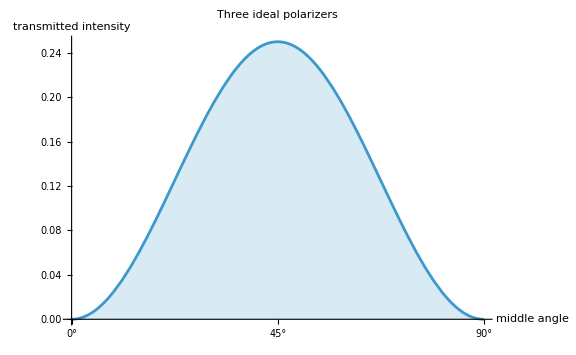

```mathematica
transmissionPlot=Plot[Evaluate[threeFilterIntensity],{θ,0,π/2},PlotRange->{0,1/4},Filling->Axis,AxesLabel->{"middle angle","transmitted intensity"},Ticks->{{{0,"0°"},{π/4,"45°"},{π/2,"90°"}},Automatic},PlotLabel->"Three ideal polarizers",ImageSize->Large]
```

## 6. Order matters

Projection matrices at different angles generally do not commute. Compare P_(45°)P_(0°)e_H with P_(0°)P_(45°)e_H. The rightmost matrix acts first.

```mathematica
p0=polarizer[0];p45=polarizer[π/4];orderedOutputs={p45.p0.horizontal,p0.p45.horizontal};orderedIntensities=FullSimplify[intensity/@orderedOutputs];{orderedOutputs,orderedIntensities}
```

({1/2,1/2} | {1/2,0}
1/2 | 1/4)

```mathematica
{p0.p45==p45.p0,p0.p45-p45.p0}
```

{False,(0 | 1/2
-1/2 | 0)}

For the same horizontal input, the two orders give intensities 1/2 and 1/4. In the first order the final polarization is at 45°. In the second, it is horizontal after a second projection. There is physical attenuation, i.e. here the ordering is not a harmless “change of coordinates” or something like that.

Do not normalize the Jones vector after each filter: doing so would erase the probability or power lost at that filter and would give the wrong final intensity. If a photon is known to have passed a particular filter, its conditional transmitted polarization may be normalized separately, but that is a different question from the total transmission through the apparatus.